FeynArts 3.11 (3 Aug 2020)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

VBSSM

{V[3],V[3]}→{V[3],V[3]}

loading generic model file /home/nyykki/FeynArts-3.11/Models/FeynArts.gen

> $GenericMixing is OFF

generic model {FeynArts} initialized

loading classes model file /home/nyykki/FeynArts-3.11/Models/FeynArts.mod

> 43 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 491 vertices

classes model {FeynArts} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 2 Generic, 3 Classes insertions

> Top. 4: 2 Generic, 3 Classes insertions

in total: 5 Generic, 7 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

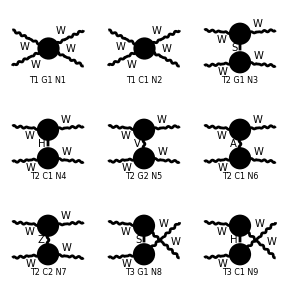

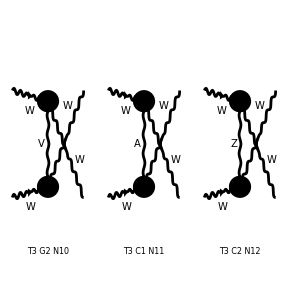

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 2 Generic, 3 Classes insertions

> Top. 4: 2 Generic, 3 Classes insertions

in total: 5 Generic, 7 Classes insertions

> Top. 1 aebf/cfde/ef.m, 0 diagrams

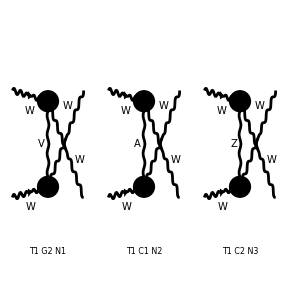

FeynArtsGraphics[{W,W}→{W,W}][([T1 G2 N1] | [T1 C1 N2] | [T1 C2 N3]
Null | Null | Null
Null | Null | Null)]

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 2 Classes amplitudes

in total: 1 Generic, 2 Classes amplitudes

preparing FORM code in /home/nyykki/fc-amp-19.frm

running FORM...

```mathematica
<<FeynArts`
<<FormCalc`tools`VecSet`


name="VBSSM"
process={V[3],V[3]}->{V[3],V[3]}
top=CreateTopologies[0,2->2];
VBStop:=InsertFields[top,process,GenericModel -> FeynArts, Model -> FeynArts];
Paint[VBStop];

vuch=DiagramDelete[VBStop,{1,2,3,4,5,6,7,8,9}];
Paint[vuch]
ampvuch=(CalcFeynAmp[CreateFeynAmp[vuch]])
res=Unabbr[ampvuch];

VecSet[1,MW,p,{0,0,1}]
VecSet[2,MW,p,{0,0,-1}]
VecSet[3,MW,p,{0,Sinθ,Cosθ}]
VecSet[4,MW,p,{0,-Sinθ,-Cosθ}]

FullSimplify[ToComponents[res,"+---"]]
```